```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

tau1.0_g2_k40_N100

Import::nffil: File not found during Import.

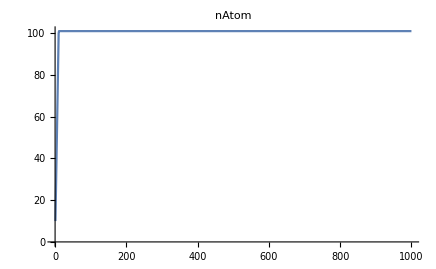

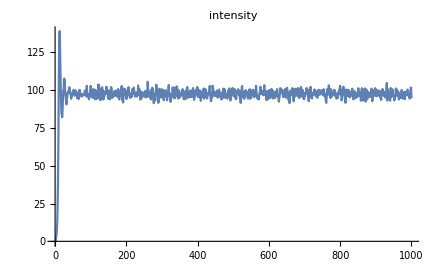

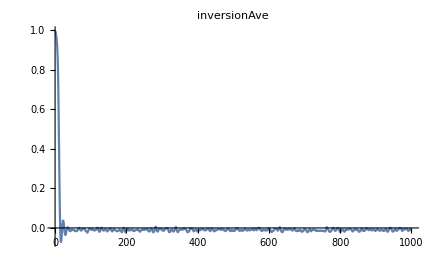

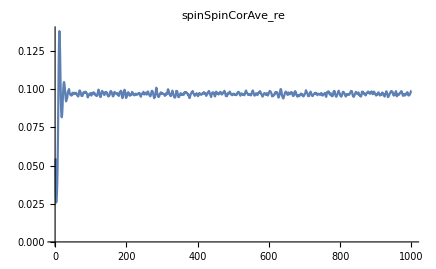

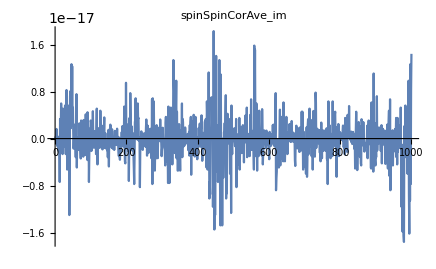

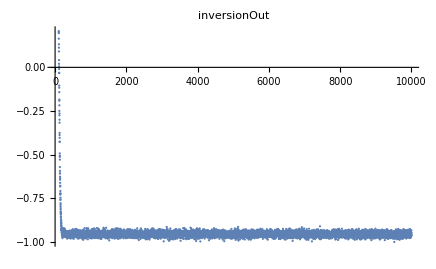

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListLinePlot[$Failed,PlotRange→All,PlotLabel→realG1]

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListLinePlot[$Failed,PlotRange→All,PlotLabel→spectra]

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCorAve_im.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-0.3,0.3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

NonlinearModelFit::fitd: First argument $Failed in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 x^2)},{linewidth,A},{x}]

NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 x^2)},{linewidth,A},{x}][ParameterTable]

ReplaceAll::reps: {NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 Power[«2»])},{linewidth,A},{x}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

linewidth/.NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 x^2)},{linewidth,A},{x}][BestFitParameters]

NonlinearModelFit::fitd: First argument $Failed in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

-Graphics-

```mathematica
tauc1=1/(linewidth1 Pi)
```

NonlinearModelFit::fitd: First argument $Failed in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 Power[«2»])},{linewidth,A},{x}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(π (linewidth/.NonlinearModelFit[$Failed,{(A linewidth)/(linewidth^2+4 x^2)},{linewidth,A},{x}][BestFitParameters]))

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

B ⅇ^(-t/tc)

NonlinearModelFit::fitd: First argument $Failed in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[$Failed,{B ⅇ^(-t/tc)},{tc,B},{t}]

NonlinearModelFit[$Failed,{B ⅇ^(-t/tc)},{tc,B},{t}][ParameterTable]

ReplaceAll::reps: {NonlinearModelFit[$Failed,{B ⅇ^(-t/tc)},{tc,B},{t}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

tc/.NonlinearModelFit[$Failed,{B ⅇ^(-t/tc)},{tc,B},{t}][BestFitParameters]

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

General::stop: Further output of Last::normal will be suppressed during this calculation.

Plot::plln: Limiting value $Failed in {x,0,$Failed} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{Plot[fitExp[x],{x,0,Last[realG1]⟦1⟧},PlotRange→All,PlotStyle→{Thickness[0.01]},BaseStyle→{FontSize→30}],},Frame→True,FrameLabel→{Time/T,G1Slow}].

Show[{Plot[fitExp[x],{x,0,Last[realG1]⟦1⟧},PlotRange→All,PlotStyle→{Thickness[0.01]},BaseStyle→{FontSize→30}],-Graphics-},Frame→True,FrameLabel→{Time/T,G1Slow}]

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

1/(π (tc/.NonlinearModelFit[$Failed,{B ⅇ^(-t/tc)},{tc,B},{t}][BestFitParameters]))

```mathematica
(*Notice there is another exponential decay.*)
```

```mathematica
cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListPlot[$Failed,PlotRange→{{0,0.06},{0,3}},PlotLabel→realG1,PlotMarkers→{Automatic,Small}]

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]].

B2 ⅇ^(-linewidthQuick π t)

NonlinearModelFit::fitd: First argument Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]],{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}]

NonlinearModelFit::fitd: First argument Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]],{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][ParameterTable]

NonlinearModelFit::fitd: First argument Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[Point[$Failed],Point[IntegerPart[0.06/($Failed⟦2,1⟧)]]].

-Graphics-

```mathematica
secondTc = 1/(linewidthQuick Pi)/.fitExp2["BestFitParameters"]
```

NonlinearModelFit::fitd: First argument Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]] in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]],{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::fitd: First argument Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]] in NonlinearModelFit is not a list or a rectangular array.

ReplaceAll::reps: {NonlinearModelFit[Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]],{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/(linewidthQuick π)/.NonlinearModelFit[Take[$Failed,IntegerPart[0.06/($Failed⟦2,1⟧)]],{B2 ⅇ^(-linewidthQuick π t)},{linewidthQuick,B2},{t}][BestFitParameters]